```mathematica
pivots[A_]:=Flatten[FirstPosition[1]/@Transpose[A]]
```

```mathematica
pMatrix[n_]:=Table[
Which[i==2&&j==1||i==1&&j==2,-1/2,
i==j&&i>2,1,
True,0],{i, n},{j,n}]
```

```mathematica
gramMatrix[W_]:=Simplify[Transpose[W].pMatrix[Length[W]].W]
```

```mathematica
linearRelationsMatrix[G_]:=RowReduce[G][[1;;MatrixRank[G]]]//Transpose
```

```mathematica
linearRelations[L_]:=Select[
Table[Equal[Subscript[b, i],L[[i]].Table[Subscript[b, i],{i,pivots[L]}]],{i,Length[L]}],Not[BooleanQ[#]]&]
```

```mathematica
linearRelationsFromW=linearRelations@*linearRelationsMatrix@*gramMatrix;
```

```mathematica
inverseLinearRelations[G_]:=Table[If[i==#,1,0],{i,Length[G[[1]]]}]&/@Flatten[FirstPosition[#,1]&/@(RowReduce[G]//Select[Not[AllTrue[#,#==0&]]&])]
```

```mathematica
quadraticFormMatrix[G_,L_]:=Inverse[Table[G[[i, j]],{i,pivots[L]},{j,pivots[L]}]]
```

```mathematica
quadraticForm[Q_,L_]:=Module[{v=Table[Subscript[b, i],{i,pivots[L]}]},Simplify[v.Q.v==0]]
```

```mathematica
quadform[W_]:=Module[{G=gramMatrix[W]},Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]]
```

```mathematica
quadformFromG[G_]:=Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]
```

```mathematica
getAlphasFromGext[Gext_,n_]:=Gext[[n+1;;-1,1;;n]]
```

```mathematica
generators[Gext_,n_]:=Block[{alphas,BigQ,G,Q,L,Li},
alphas=getAlphasFromGext[Gext,n];
G=Gext[[1;;n,1;;n]];
L=linearRelationsMatrix[G];
Q=quadraticFormMatrix[G,L];
Li=inverseLinearRelations[G];
BigQ=Transpose[Li].Q.Li;
alphas=Table[{#}&/@alpha,{alpha,alphas}];
(IdentityMatrix[n]-2(#.Transpose[#]).BigQ)&/@alphas]
```

```mathematica
G=gramMatrix[W]
```

{{1,-1,-1,-1,-1,-3},{-1,1,-1,-1,-3,-1},{-1,-1,1,-3,-1,-1},{-1,-1,-3,1,-1,-1},{-1,-3,-1,-1,1,-1},{-3,-1,-1,-1,-1,1}}

```mathematica
sigmas=findGeneratorsFromG[G]
```

{{{1,0,0,0,0,0},{0,1,0,0,0,0},{3,4,0,3,0,-1},{0,0,0,1,0,0},{3,3,0,4,0,-1},{2,4,0,4,0,-1}},{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{4,4,2,-1,0,0},{4,3,3,-1,0,0},{3,4,3,-1,0,0}},{{1,0,0,0,0,0},{4,0,-1,3,3,0},{4,0,-1,2,4,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{3,0,-1,3,4,0}},{{1,0,0,0,0,0},{4,0,3,-1,3,0},{0,0,1,0,0,0},{4,0,2,-1,4,0},{0,0,0,0,1,0},{3,0,3,-1,4,0}},{{0,3,4,0,-1,3},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,3,3,0,-1,4},{0,2,4,0,-1,4},{0,0,0,0,0,1}},{{0,4,-1,3,0,3},{0,1,0,0,0,0},{0,4,-1,2,0,4},{0,0,0,1,0,0},{0,3,-1,3,0,4},{0,0,0,0,0,1}},{{0,-1,4,0,3,3},{0,-1,4,0,2,4},{0,0,1,0,0,0},{0,-1,3,0,3,4},{0,0,0,0,1,0},{0,0,0,0,0,1}},{{0,-1,0,4,3,3},{0,-1,0,4,2,4},{0,-1,0,3,3,4},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}}

```mathematica
MatrixForm[L=linearRelationsMatrix[G]]
```

Part::span: 1;;MatrixRank[Transpose[W].{}.W] is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Transpose[RowReduce[Transpose[W].{}.W]⟦1;;MatrixRank[Transpose[W].{}.W]⟧]

```mathematica
MatrixForm[Li=inverseLinearRelations[G]]
```

RowReduce::argx: RowReduce called with 0 arguments; 1 argument is expected.

RowReduce[]

```mathematica
L.Li.{-1,2,4,10,12,15}
```

Transpose[RowReduce[Transpose[W].{}.W]⟦1;;MatrixRank[Transpose[W].{}.W]⟧].RowReduce[].{-1,2,4,10,12,15}

```mathematica
L.Li//MatrixForm
```

Transpose[RowReduce[Transpose[W].{}.W]⟦1;;MatrixRank[Transpose[W].{}.W]⟧].RowReduce[]

```mathematica
Li.L//MatrixForm
```

RowReduce[].Transpose[RowReduce[Transpose[W].{}.W]⟦1;;MatrixRank[Transpose[W].{}.W]⟧]

```mathematica
sigmas=generators[{{1, -1, -1, -1, -1, -3, 0, 0, 0, -2Sqrt[2], -2Sqrt[2], 0, -2Sqrt[2], -2Sqrt[2]}, {-1, 1, -1, -3, -1, -1, 0, -2Sqrt[2], -2Sqrt[2], -2Sqrt[2], 0, 0, -2Sqrt[2], 0}, {-1, -1, 1, -1, -3, -1, 0, -2Sqrt[2], 0, 0, 0, -2Sqrt[2], -2Sqrt[2], -2Sqrt[2]}, {-1, -3, -1, 1, -1, -1, -2Sqrt[2], 0, 0, 0, -2Sqrt[2], -2Sqrt[2], 0, -2Sqrt[2]}, {-1, -1, -3, -1, 1, -1, -2Sqrt[2], 0, -2Sqrt[2], -2Sqrt[2], -2Sqrt[2], 0, 0, 0}, {-3, -1, -1, -1, -1, 1, -2Sqrt[2], -2Sqrt[2], -2Sqrt[2], 0, 0, -2Sqrt[2], 0, 0}, {0, 0, 0, -2Sqrt[2], -2Sqrt[2], -2Sqrt[2], 1, -3, -1, -3, -1, -1, -5, -3}, {0, -2Sqrt[2], -2Sqrt[2], 0, 0, -2Sqrt[2], -3, 1, -1, -3, -5, -1, -1, -3}, {0, -2Sqrt[2], 0, 0, -2Sqrt[2], -2Sqrt[2], -1, -1, 1, -1, -3, -3, -3, -5}, {-2Sqrt[2], -2Sqrt[2], 0, 0, -2Sqrt[2], 0, -3, -3, -1, 1, -1, -5, -1, -3}, {-2Sqrt[2], 0, 0, -2Sqrt[2], -2Sqrt[2], 0, -1, -5, -3, -1, 1, -3, -3, -1}, {0, 0, -2Sqrt[2], -2Sqrt[2], 0, -2Sqrt[2], -1, -1, -3, -5, -3, 1, -3, -1}, {-2Sqrt[2], -2Sqrt[2], -2Sqrt[2], 0, 0, 0, -5, -1, -3, -1, -3, -3, 1, -1}, {-2Sqrt[2], 0, -2Sqrt[2], -2Sqrt[2], 0, 0, -3, -3, -5, -3, -1, -1, -1, 1}},6]
```

{{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{4,2,4,-1,0,0},{4,2,4,-2,1,0},{4,2,4,-2,0,1}},{{1,0,0,0,0,0},{4,3,-4,6,0,0},{4,2,-3,6,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{4,2,-4,6,0,1}},{{1,0,0,0,0,0},{4,-1,4,2,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{4,-2,4,2,1,0},{4,-2,4,2,0,1}},{{-3,2,4,6,0,0},{-4,3,4,6,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{-4,2,4,6,1,0},{0,0,0,0,0,1}},{{-3,6,4,2,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{-4,6,4,3,0,0},{-4,6,4,2,1,0},{0,0,0,0,0,1}},{{1,0,0,0,0,0},{0,1,0,0,0,0},{4,6,-3,2,0,0},{4,6,-4,3,0,0},{0,0,0,0,1,0},{4,6,-4,2,0,1}},{{-3,6,-4,10,0,0},{-4,7,-4,10,0,0},{-4,6,-3,10,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},{{-3,10,-4,6,0,0},{0,1,0,0,0,0},{-4,10,-3,6,0,0},{-4,10,-4,7,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}}

```mathematica
Print[MatrixForm[#]]&/@sigmas;
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
4 | 2 | 4 | -1 | 0 | 0
4 | 2 | 4 | -2 | 1 | 0
4 | 2 | 4 | -2 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0
4 | 3 | -4 | 6 | 0 | 0
4 | 2 | -3 | 6 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
4 | 2 | -4 | 6 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0
4 | -1 | 4 | 2 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
4 | -2 | 4 | 2 | 1 | 0
4 | -2 | 4 | 2 | 0 | 1)

(-3 | 2 | 4 | 6 | 0 | 0
-4 | 3 | 4 | 6 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
-4 | 2 | 4 | 6 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

(-3 | 6 | 4 | 2 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
-4 | 6 | 4 | 3 | 0 | 0
-4 | 6 | 4 | 2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
4 | 6 | -3 | 2 | 0 | 0
4 | 6 | -4 | 3 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
4 | 6 | -4 | 2 | 0 | 1)

(-3 | 6 | -4 | 10 | 0 | 0
-4 | 7 | -4 | 10 | 0 | 0
-4 | 6 | -3 | 10 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

(-3 | 10 | -4 | 6 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
-4 | 10 | -3 | 6 | 0 | 0
-4 | 10 | -4 | 7 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
sigmas[[5]].{2,2,7,4,-1,4}
```

{42,2,7,44,39,4}

```mathematica
allData[G_]:={quadformFromG[G],linearRelations[linearRelationsMatrix[G]]}
```

Not my code; no clue how it works

```mathematica
nextCandidate[s_,t_,adj_]:=Block[{length,pos},length=Length[adj];
pos=Mod[Position[adj,s][[1,1]]+1,length,1];
{t,adj[[pos]]}];
```

```mathematica
FindFace[g_?PlanarGraphQ]:=Block[{emb},emb=GraphEmbedding[g,"PlanarEmbedding"];
FindFace[g,emb]];

FindFace[g_?PlanarGraphQ,emb_]:=Block[{m,orderings,pAdj,rightF,s,t,initial,face},m=AdjacencyMatrix[g];
Table[pAdj[v]=SortBy[Pick[VertexList[g],m[[v]],1],ArcTan@@(emb[[v]]-emb[[#]])&],{v,VertexList[g]}];
rightF[_]:=False;
Reap[Table[If[!rightF[e],s=e[[1]];
t=e[[2]];
initial=s;
face={s};
While[t=!=initial,rightF[UndirectedEdge[s,t]]=True;
{s,t}=nextCandidate[s,t,pAdj[t]];
face=Join[face,{s}];];
Sow[face];],{e,EdgeList[g]}]][[2,1]]]
```

```mathematica
MatrixForm[W={{2, 2, -1, 7, 4, 4}, {0, 0, 1, 1, 2, 2}, {0, 0, 0, 2Sqrt[2], 2Sqrt[2], 2Sqrt[2]}, {1, -1, 0, 0, 1, -1}}]
```

(2 | 2 | -1 | 7 | 4 | 4
0 | 0 | 1 | 1 | 2 | 2
0 | 0 | 0 | 2 √2 | 2 √2 | 2 √2
1 | -1 | 0 | 0 | 1 | -1)

```mathematica
bt=2(2+Sqrt[3])
b=1/(2+Sqrt[3])
```

2 (2+√3)

1/(2+√3)

```mathematica
W = {{2, 2, 2, 2, 2, 2, 2, 2, bt, bt, bt, bt, bt, bt, bt, bt}, {1, 1, 1, 1, 1, 1, 1, 1, b, b, b, b, b, b, b, b}, {1, 1, 1, 1, -1, -1, -1, -1, 1, 1, 1, 1, -1, -1, -1, -1}, {1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1}, {1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1}}
```

{{2,2,2,2,2,2,2,2,2 (2+√3),2 (2+√3),2 (2+√3),2 (2+√3),2 (2+√3),2 (2+√3),2 (2+√3),2 (2+√3)},{1,1,1,1,1,1,1,1,1/(2+√3),1/(2+√3),1/(2+√3),1/(2+√3),1/(2+√3),1/(2+√3),1/(2+√3),1/(2+√3)},{1,1,1,1,-1,-1,-1,-1,1,1,1,1,-1,-1,-1,-1},{1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1},{1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1}}

```mathematica
b=.;bt=.
```

```mathematica
MatrixForm[G=gramMatrix[W]]
```

(1 | -1 | -1 | -3 | -1 | -3 | -3 | -5 | -1 | -3 | -3 | -5 | -3 | -5 | -5 | -7
-1 | 1 | -3 | -1 | -3 | -1 | -5 | -3 | -3 | -1 | -5 | -3 | -5 | -3 | -7 | -5
-1 | -3 | 1 | -1 | -3 | -5 | -1 | -3 | -3 | -5 | -1 | -3 | -5 | -7 | -3 | -5
-3 | -1 | -1 | 1 | -5 | -3 | -3 | -1 | -5 | -3 | -3 | -1 | -7 | -5 | -5 | -3
-1 | -3 | -3 | -5 | 1 | -1 | -1 | -3 | -3 | -5 | -5 | -7 | -1 | -3 | -3 | -5
-3 | -1 | -5 | -3 | -1 | 1 | -3 | -1 | -5 | -3 | -7 | -5 | -3 | -1 | -5 | -3
-3 | -5 | -1 | -3 | -1 | -3 | 1 | -1 | -5 | -7 | -3 | -5 | -3 | -5 | -1 | -3
-5 | -3 | -3 | -1 | -3 | -1 | -1 | 1 | -7 | -5 | -5 | -3 | -5 | -3 | -3 | -1
-1 | -3 | -3 | -5 | -3 | -5 | -5 | -7 | 1 | -1 | -1 | -3 | -1 | -3 | -3 | -5
-3 | -1 | -5 | -3 | -5 | -3 | -7 | -5 | -1 | 1 | -3 | -1 | -3 | -1 | -5 | -3
-3 | -5 | -1 | -3 | -5 | -7 | -3 | -5 | -1 | -3 | 1 | -1 | -3 | -5 | -1 | -3
-5 | -3 | -3 | -1 | -7 | -5 | -5 | -3 | -3 | -1 | -1 | 1 | -5 | -3 | -3 | -1
-3 | -5 | -5 | -7 | -1 | -3 | -3 | -5 | -1 | -3 | -3 | -5 | 1 | -1 | -1 | -3
-5 | -3 | -7 | -5 | -3 | -1 | -5 | -3 | -3 | -1 | -5 | -3 | -1 | 1 | -3 | -1
-5 | -7 | -3 | -5 | -3 | -5 | -1 | -3 | -3 | -5 | -1 | -3 | -1 | -3 | 1 | -1
-7 | -5 | -5 | -3 | -5 | -3 | -3 | -1 | -5 | -3 | -3 | -1 | -3 | -1 | -1 | 1)

```mathematica
linearRelationsMatrix[G]//pivots
```

{1,2,3,5,9}

```mathematica
linearRelationsMatrix[G]//linearRelations//Column
```

b_4==-b_1+b_2+b_3
b_6==-b_1+b_2+b_5
b_7==-b_1+b_3+b_5
b_8==-2 b_1+b_2+b_3+b_5
b_10==-b_1+b_2+b_9
b_11==-b_1+b_3+b_9
b_12==-2 b_1+b_2+b_3+b_9
b_13==-b_1+b_5+b_9
b_14==-2 b_1+b_2+b_5+b_9
b_15==-2 b_1+b_3+b_5+b_9
b_16==-3 b_1+b_2+b_3+b_5+b_9

```mathematica
(Q=quadraticFormMatrix[G,linearRelationsMatrix[G]])//MatrixForm
```

(2/3 | -1/12 | -1/12 | -1/12 | -1/12
-1/12 | 1/6 | -1/12 | -1/12 | -1/12
-1/12 | -1/12 | 1/6 | -1/12 | -1/12
-1/12 | -1/12 | -1/12 | 1/6 | -1/12
-1/12 | -1/12 | -1/12 | -1/12 | 1/6)

```mathematica
quadraticForm[Q,linearRelationsMatrix[G]]
```

4 b_1^2+b_2^2+b_3^2+b_5^2+b_9^2==b_3 b_5+b_3 b_9+b_5 b_9+b_2 (b_3+b_5+b_9)+b_1 (b_2+b_3+b_5+b_9)

```mathematica
Table[G[[i,j]],{i,pivots[linearRelationsMatrix[G]]},{j,pivots[linearRelationsMatrix[G]]}]//MatrixForm
```

(1 | -1 | -1 | -1 | -1
-1 | 1 | -3 | -3 | -3
-1 | -3 | 1 | -3 | -3
-1 | -3 | -3 | 1 | -3
-1 | -3 | -3 | -3 | 1)

```mathematica
quadform[W]//Expand
```

4 b_1^2+b_2^2+b_3^2+b_5^2+b_9^2==b_1 b_2+b_1 b_3+b_2 b_3+b_1 b_5+b_2 b_5+b_3 b_5+b_1 b_9+b_2 b_9+b_3 b_9+b_5 b_9

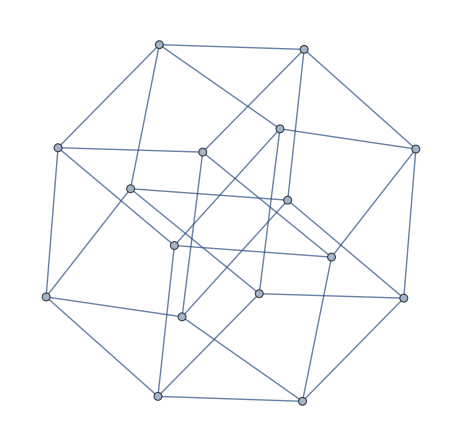

```mathematica
AdjacencyGraph[If[#==-1,1,0]&/@#&/@G]
```

```mathematica
quadformFromG[G]
```

4 b_1^2+b_2^2+b_3^2+b_5^2+b_9^2==b_3 b_5+b_3 b_9+b_5 b_9+b_2 (b_3+b_5+b_9)+b_1 (b_2+b_3+b_5+b_9)

```mathematica
Subscript[G, triangular bipyramidal]={{1, -1, -1, -1, -7}, {-1, 1, -1, -1, -1}, {-1, -1, 1, -1, -1}, {-1, -1, -1, 1, -1}, {-7, -1, -1, -1, 1}}
```

{{1,-1,-1,-1,-7},{-1,1,-1,-1,-1},{-1,-1,1,-1,-1},{-1,-1,-1,1,-1},{-7,-1,-1,-1,1}}

```mathematica
quadformFromG[Subscript[G, triangular bipyramidal]]
```

b_1^2+b_2^2+(b_3-b_4)^2==2 b_2 (b_3+b_4)+2 b_1 (b_2+b_3+b_4)

```mathematica
linearRelations[linearRelationsMatrix[Subscript[G, triangular bipyramidal]]]//Column
```

b_5==-b_1+2 b_2+2 b_3+2 b_4

```mathematica
Subscript[G, 6v7f2]={{1, -1, -5, -1, -1, -1}, {-1, 1, -1, -1, -5, -1}, {-5, -1, 1, -1, -7, -1}, {-1, -1, -1, 1, -1, -5/3}, {-1, -5, -7, -1, 1, -1}, {-1, -1, -1, -5/3, -1, 1}}
```

{{1,-1,-5,-1,-1,-1},{-1,1,-1,-1,-5,-1},{-5,-1,1,-1,-7,-1},{-1,-1,-1,1,-1,-5/3},{-1,-5,-7,-1,1,-1},{-1,-1,-1,-5/3,-1,1}}

```mathematica
quadformFromG[Subscript[G, 6v7f2]]
```

b_1^2+9 b_2^2+(b_3-3 b_4)^2==6 b_2 (b_3-b_4)+2 b_1 (3 b_2+b_3+3 b_4)

```mathematica
linearRelations[linearRelationsMatrix[Subscript[G, 6v7f2]]]//Column
```

b_5==2 b_1-2 b_2+b_3
b_6==(2 b_1)/3-(2 b_2)/3+(2 b_3)/3-b_4

```mathematica
quadformFromG[{{1, -1, -1, -1}, {-1, 1, -1, -1}, {-1, -1, 1, -1}, {-1, -1, -1, 1}}]
```

b_1^2+b_2^2+(b_3-b_4)^2==2 b_2 (b_3+b_4)+2 b_1 (b_2+b_3+b_4)

```mathematica
Subscript[G, hexagonal pyramid]={{1, -1, -5, -7, -5, -1, -1}, {-1, 1, -1, -5, -7, -5, -1}, {-5, -1, 1, -1, -5, -7, 1}, {-7, -5, -1, 1, -1, -5, -1}, {-5, -7, -5, -1, 1, -1, -1}, {-1, -5, -7, -5, -1, 1, -1}, {-1, -1, -1, -1, -1, -1, 1}}
```

{{1,-1,-5,-7,-5,-1,-1},{-1,1,-1,-5,-7,-5,-1},{-5,-1,1,-1,-5,-7,1},{-7,-5,-1,1,-1,-5,-1},{-5,-7,-5,-1,1,-1,-1},{-1,-5,-7,-5,-1,1,-1},{-1,-1,-1,-1,-1,-1,1}}

```mathematica
allData[Subscript[G, hexagonal pyramid]][[1]]//Expand
```

6 b_2^2-5 b_2 b_3+b_3^2+9 b_2 b_7-6 b_3 b_7+9 b_7^2==4 b_1 b_2+b_1 b_3+3 b_1 b_7

```mathematica
allData[Subscript[G, hexagonal pyramid]][[2]]//Column
```

b_4==b_1-2 b_2+2 b_3
b_5==2 b_1-3 b_2+2 b_3
b_6==2 b_1-2 b_2+b_3

```mathematica
W={{2, 2, -1, 7, 4, 4}, {0, 0, 1, 1, 2, 2}, {0, 0, 0, 2Sqrt[2], 2Sqrt[2], 2Sqrt[2]}, {1, -1, 0, 0, 1, -1}}
```

{{2,2,-1,7,4,4},{0,0,1,1,2,2},{0,0,0,2 √2,2 √2,2 √2},{1,-1,0,0,1,-1}}

```mathematica
G=gramMatrix[W];
```

```mathematica
G
```

{{1,-1,-1,-1,-1,-3},{-1,1,-1,-1,-3,-1},{-1,-1,1,-3,-1,-1},{-1,-1,-3,1,-1,-1},{-1,-3,-1,-1,1,-1},{-3,-1,-1,-1,-1,1}}

```mathematica
G={{1, -3, -1, -3, -1, -1, -5, -3}, {-3, 1, -1, -3, -5, -1, -1, -3}, {-1, -1, 1, -1, -3, -3, -3, -5}, {-3, -3, -1, 1, -1, -5, -1, -3}, {-1, -5, -3, -1, 1, -3, -3, -1}, {-1, -1, -3, -5, -3, 1, -3, -1}, {-5, -1, -3, -1, -3, -3, 1, -1}, {-3, -3, -5, -3, -1, -1, -1, 1}}
```

{{1,-3,-1,-3,-1,-1,-5,-3},{-3,1,-1,-3,-5,-1,-1,-3},{-1,-1,1,-1,-3,-3,-3,-5},{-3,-3,-1,1,-1,-5,-1,-3},{-1,-5,-3,-1,1,-3,-3,-1},{-1,-1,-3,-5,-3,1,-3,-1},{-5,-1,-3,-1,-3,-3,1,-1},{-3,-3,-5,-3,-1,-1,-1,1}}

```mathematica
linearRelationsMatrix[G]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | -1 | 1
1 | 1 | -1 | 0
0 | 1 | -1 | 1
1 | 1 | -2 | 1)

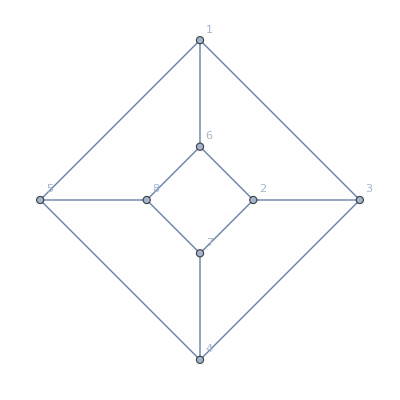

```mathematica
g=PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]
```

```mathematica
faces=FindFace[g]
```

{{1,3,4,5},{1,5,8,6},{1,6,2,3},{2,6,8,7},{2,7,4,3},{4,7,8,5}}

```mathematica
findGenerators[faces_,vertices_,G_]:=Table[Block[{face,otherVertex,verticesOnFace,allVertices,Gp,P,Gnew,L,Q,Qform,sol1,sol2,sols,coeff,coeffTable,small,Li,P2},
face=faces[[i]];
verticesOnFace=Sort[RandomSample[face,3]];
otherVertex=RandomChoice[Select[vertices,Not[MemberQ[face,#]]&]];
allVertices=Append[verticesOnFace,otherVertex];
P=Transpose[IdentityMatrix[Length[vertices]][[#]]&/@DeleteDuplicates[Join[allVertices,vertices]]];
Gnew=Transpose[P].G.P;
L=linearRelationsMatrix[Gnew];
Gp=Table[G[[i,j]],{i,allVertices},{j,allVertices}];
Q=Inverse[Gp];
Qform=(#.Q.#&[Table[Subscript[b, j],{j,allVertices}]])==0;
sols=Expand[FullSimplify[Total[#[[1]][[2]]&/@Solve[Qform,Subscript[b, otherVertex]]]]];
coeff=Table[sols/.Table[Subscript[b, i]->If[i==curr,1,0],{i,allVertices}],{curr,allVertices}];
small=IdentityMatrix[Length[allVertices]];
small[[-1]]=Table[If[j==4,-1,If[MemberQ[verticesOnFace,allVertices[[j]]],coeff[[j]],0]],{j,Length[allVertices]}];
Li=Table[Table[If[j==k,1,0],{j,Length[vertices]}],{k,allVertices}];
P2=Table[If[j==k,1,0],{j,Length[vertices]},{k,DeleteDuplicates[Join[allVertices,vertices]]}];
P2.L.small.Li
],{i,Length[faces]}]
```

```mathematica
findGeneratorsFromG[G_]:=findGenerators[FindFace[PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]],Range[Length[G]],G]
```

```mathematica
Print[MatrixForm[#]]&/@findGeneratorsFromG[G]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 3 | 0 | 0 | -1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 2 | 0 | 3 | 0 | 0 | -1
-1 | 0 | 3 | 0 | 4 | 0 | 0 | -1
0 | 0 | 2 | 0 | 4 | 0 | 0 | -1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | -1 | 0 | -1 | 4
3 | 0 | 0 | 0 | 0 | 0 | -1 | 3
2 | 0 | 0 | 0 | 1 | 0 | -1 | 3
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | -1 | 0 | 0 | 1
2 | 0 | 0 | 0 | 0 | 0 | -1 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
3 | 2 | 1 | 0 | -1 | 0 | 0 | 0
4 | 2 | 0 | 0 | -1 | 0 | 0 | 0
1 | 1 | -1 | 0 | 0 | 0 | 0 | 0
3 | 3 | 0 | 0 | -1 | 0 | 0 | 0
4 | 3 | -1 | 0 | -1 | 0 | 0 | 0)

(0 | 3 | 0 | -1 | 0 | 0 | 0 | 3
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | -1 | 0 | 0 | 1 | 2
0 | 2 | 0 | -1 | 0 | 0 | 2 | 2
0 | 2 | 0 | -1 | 0 | 0 | 1 | 3
0 | 1 | 0 | 0 | 0 | 0 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(0 | -1 | 4 | 0 | -1 | 0 | 3 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 1 | 0
0 | -2 | 4 | 0 | -1 | 0 | 4 | 0
0 | 0 | 3 | 0 | -1 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 3 | 0 | -1 | 0 | 4 | 0)

(0 | 0 | 0 | 3 | 0 | -1 | -1 | 4
0 | 0 | 0 | 2 | 0 | -1 | 1 | 3
0 | 0 | 0 | 3 | 0 | -1 | 0 | 3
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | 1
0 | 0 | 0 | 2 | 0 | -1 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{Null,Null,Null,Null,Null,Null}